ParametricFunction[<>]

ParametricNDSolveValue::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

{{InterpolatingFunction[…],InterpolatingFunction[…]},{}}

-0.760836

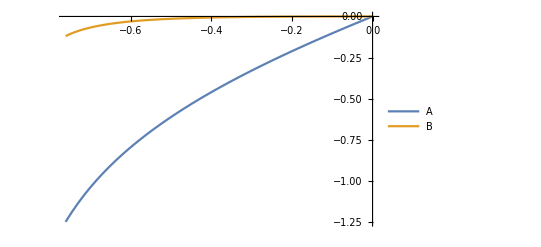

```mathematica
(*Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];*)
zmax=2.; (*Trigger value to stop integration of background solution *)

(* Numerically solve ODEs for cosmic expansion. ParametricNDSolveValue does "setup" for ODEs but does not actually integrate them until called with a specific set of parameters.*)
ABvacmetric0=ParametricNDSolveValue[
{ⅇ^(-4 AA0[τ]+4 BB0[τ]) ΩB+ⅇ^(-2 AA0[τ]+2 BB0[τ]) Ωk+ⅇ^(-3 AA0[τ]) Ωm+ⅇ^(-4 AA0[τ]) Ωr+ΩΛ-AA0'[τ]^2+BB0'[τ]^2==0,ⅇ^(-4 AA0[τ]+4 BB0[τ]) ΩB+ⅇ^(-2 AA0[τ]+2 BB0[τ]) Ωk-1/3 ⅇ^(-4 AA0[τ]) Ωr+ΩΛ-AA0'[τ]^2+2 AA0'[τ] BB0'[τ]-BB0'[τ]^2-(2 AA0''[τ])/3+(2 BB0''[τ])/3==0,
WhenEvent[AA0'[τ]+2BB0'[τ]==0, Sow[True]; "StopIntegration"],(* Set flag to "True" & stop if we get to a contracting phase *)
WhenEvent[Min[Exp[-(AA0[τ]+2BB0[τ])]-1,Exp[-(AA0[τ]-BB0[τ])]-1]>zmax+0.1,"StopIntegration"],
(* Stop if we get to z = zmax in all directions without entering a contracting phase *)
AA0[0]==BB0[0]==AA0'[0]-1==BB0'[0]-b0==0},{AA0,BB0},{τ,-∞,0},{ΩB,Ωk,Ωm,Ωr,ΩΛ,b0},Method->{"ParametricSensitivity"->None}]

currentpt = {0.01,0.01,0.28,0.01,0.69,0,0.7};
{{currentA,currentB},contractflag}=ABvacmetric0@(Sequence@@Take[currentpt,6])//Reap
earlytime=currentA["Domain"][[1,1]]

Plot[{currentA[x], currentB[x]}, {x, earlytime, 0}, PlotLegends -> {"A", "B"}]
```

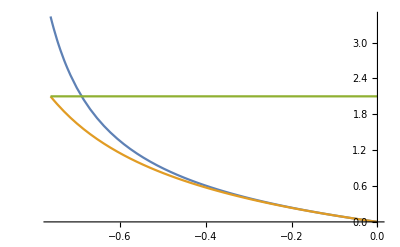

```mathematica
Plot[{Exp[-(currentA[τ]+2currentB[τ])]-1,Exp[-(currentA[τ]-currentB[τ])]-1,zmax+0.1},{τ,earlytime,0}]
```